```mathematica
ClearCookies
```

ClearCookies

```mathematica
a=8;
b=6;
c=4;
```

```mathematica
x=a*Sin[u]Cos[v];
y=b*Sin[u]Sin[v];
z=c*Cos[u];
```

```mathematica
S1=ParametricPlot3D[{x,y,z},{u,0,Pi},{v,0,2Pi},MeshStyle->None,PlotStyle->Opacity[0.5],BoxRatios->Automatic,Axes->False]
```

-Graphics3D-

```mathematica
σu={D[x,u],D[y,u],D[z,u]};
σv={D[x,v],D[y,v],D[z,v]};
```

```mathematica
σuu=D[σu,u];
σuv=D[σu,v];
σvv=D[σv,v];
```

```mathematica
nn=Cross[σu,σv]/Norm[Cross[σu,σv]];
```

```mathematica
e=σu.σu;
f=σu.σv;
g=σv.σv;
```

```mathematica
l=σuu.nn;
m=σuv.nn;
n=σvv.nn;
```

```mathematica
λ1=l/e;
```

```mathematica
λ2=n/g;
```

```mathematica
λ11=λ1/.{u->Pi/10,v->Pi};
λ12=λ1/.{u->2*Pi/10,v->Pi};
λ13=λ1/.{u->3*Pi/10,v->Pi};
λ14=λ1/.{u->4*Pi/10,v->Pi};
λ15=λ1/.{u->5*Pi/10,v->Pi};
λ16=λ1/.{u->6*Pi/10,v->Pi};
λ17=λ1/.{u->7*Pi/10,v->Pi};
λ18=λ1/.{u->8*Pi/10,v->Pi};
λ19=λ1/.{u->9*Pi/10,v->Pi};
```

```mathematica
λ21=λ2/.{u->Pi/10,v->Pi};
λ22=λ2/.{u->2*Pi/10,v->Pi};
λ23=λ2/.{u->3*Pi/10,v->Pi};
λ24=λ2/.{u->4*Pi/10,v->Pi};
λ25=λ2/.{u->5*Pi/10,v->Pi};
λ26=λ2/.{u->6*Pi/10,v->Pi};
λ27=λ2/.{u->7*Pi/10,v->Pi};
λ28=λ2/.{u->8*Pi/10,v->Pi};
λ29=λ2/.{u->9*Pi/10,v->Pi};
```

```mathematica
c11=ContourPlot[{λ1==λ11,λ2==λ21},{u,0,Pi},{v,0,2*Pi}];
c12=ContourPlot[{λ1==λ12,λ2==λ22},{u,0,Pi},{v,0,2*Pi}];
c13=ContourPlot[{λ1==λ13,λ2==λ23},{u,0,Pi},{v,0,2*Pi}];
c14=ContourPlot[{λ1==λ14,λ2==λ24},{u,0,Pi},{v,0,2*Pi}];
c15=ContourPlot[{λ1==λ15,λ2==λ25},{u,0,Pi},{v,0,2*Pi}];
c16=ContourPlot[{λ1==λ16,λ2==λ26},{u,0,Pi},{v,0,2*Pi}];
c17=ContourPlot[{λ1==λ17,λ2==λ27},{u,0,Pi},{v,0,2*Pi}];
c18=ContourPlot[{λ1==λ18,λ2==λ28},{u,0,Pi},{v,0,2*Pi}];
c19=ContourPlot[{λ1==λ19,λ2==λ29},{u,0,Pi},{v,0,2*Pi}];
```

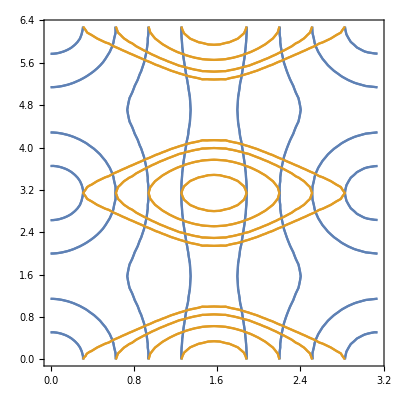

```mathematica
Show[{c11,c12,c13,c14,c15,c16,c17,c18,c19},AspectRatio->1/1,Axes->False]
```